```mathematica
RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]
```

115

115

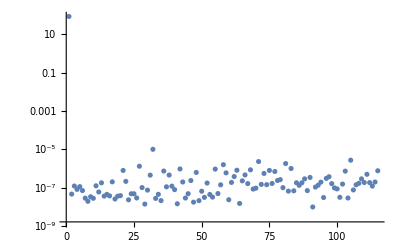

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False
]
```

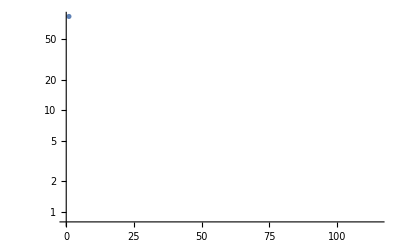

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0.8,All},
Joined->False
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|L0BPhaseSet→2.27268,L1PhaseSet→-21.8706,L2PhaseSet→-39.4275,L3PhaseSet→2.5645,S1EL_xOffset→0.0020518,S1EL_yOffset→-0.000134509,S2EL_xOffset→-0.00217136,S2EL_yOffset→0.00027144,S2ER_xOffset→-0.00128878,S2ER_yOffset→-0.000292177,S1ER_xOffset→0.00372248,S1ER_yOffset→-0.000183846,XC1FFkG→0.0538854,XC3FFkG→-0.0171606,YC1FFkG→-0.00250771,YC2FFkG→-0.0307077,PDrive_mean_x→8.4789×10^-6,PDrive_mean_y→-1.312×10^-7,PDrive_sigma_x→0.000040218,PDrive_sigma_y→0.0000201887,PDrive_mean_xp→0.0000868932,PDrive_mean_yp→-0.000158947,PDrive_median_x→3.1732×10^-6,PDrive_median_y→2.361×10^-7,PDrive_median_xp→0.00020157,PDrive_median_yp→-0.000152892,PDrive_sigmaSI90_x→0.0000279384,PDrive_sigmaSI90_y→0.0000186138,PDrive_sigmaSI90_z→0.0000242781,PDrive_emitSI90_x→0.000139108,PDrive_emitSI90_y→9.018×10^-6,PDrive_zCentroid→991.332,PWitness_mean_x→-1.6224×10^-6,PWitness_mean_y→-2.2211×10^-6,PWitness_sigma_x→0.0000197809,PWitness_sigma_y→0.0000228719,PWitness_mean_xp→-0.0000634532,PWitness_mean_yp→-0.00014127,PWitness_median_x→-3.386×10^-7,PWitness_median_y→-1.6867×10^-6,PWitness_median_xp→-0.0000571656,PWitness_median_yp→-0.000140902,PWitness_sigmaSI90_x→0.0000185651,PWitness_sigmaSI90_y→0.0000211217,PWitness_sigmaSI90_z→0.0000156979,PWitness_emitSI90_x→0.0000124436,PWitness_emitSI90_y→3.7522×10^-6,PWitness_zCentroid→991.332,bunchSpacing→0.000142195,transverseCentroidOffset→0.0000103152,lostChargeFraction→0.,errorTerm_lostChargeFraction→0.,errorTerm_bunchSpacing→0.,errorTerm_transverseOffset→0.,errorTerm_angleOffset→0.,errorTerm_mainObjective→0.0713013,maximizeMe→84.1499|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

L0BPhaseSet : 2.272679177
L1PhaseSet : -21.8706147942
L2PhaseSet : -39.427461647
L3PhaseSet : 2.5644990507
S1EL_xOffset : 0.0020517993
S1EL_yOffset : -0.0001345092
S2EL_xOffset : -0.0021713604
S2EL_yOffset : 0.0002714401
S2ER_xOffset : -0.0012887764
S2ER_yOffset : -0.0002921767
S1ER_xOffset : 0.0037224836
S1ER_yOffset : -0.000183846
XC1FFkG : 0.0538853769
XC3FFkG : -0.0171605603
YC1FFkG : -0.0025077111
YC2FFkG : -0.0307077009
PDrive_mean_x : 8.4789e-6
PDrive_mean_y : -1.312e-7
PDrive_sigma_x : 0.000040218
PDrive_sigma_y : 0.0000201887
PDrive_mean_xp : 0.0000868932
PDrive_mean_yp : -0.000158947
PDrive_median_x : 3.1732e-6
PDrive_median_y : 2.361e-7
PDrive_median_xp : 0.0002015703
PDrive_median_yp : -0.0001528923
PDrive_sigmaSI90_x : 0.0000279384
PDrive_sigmaSI90_y : 0.0000186138
PDrive_sigmaSI90_z : 0.0000242781
PDrive_emitSI90_x : 0.0001391076
PDrive_emitSI90_y : 9.018e-6
PDrive_zCentroid : 991.3316894236
PWitness_mean_x : -1.6224e-6
PWitness_mean_y : -2.2211e-6
PWitness_sigma_x : 0.0000197809
PWitness_sigma_y : 0.0000228719
PWitness_mean_xp : -0.0000634532
PWitness_mean_yp : -0.0001412702
PWitness_median_x : -3.386e-7
PWitness_median_y : -1.6867e-6
PWitness_median_xp : -0.0000571656
PWitness_median_yp : -0.000140902
PWitness_sigmaSI90_x : 0.0000185651
PWitness_sigmaSI90_y : 0.0000211217
PWitness_sigmaSI90_z : 0.0000156979
PWitness_emitSI90_x : 0.0000124436
PWitness_emitSI90_y : 3.7522e-6
PWitness_zCentroid : 991.3318316181
bunchSpacing : 0.0001421945
transverseCentroidOffset : 0.0000103152
lostChargeFraction : 0.
errorTerm_lostChargeFraction : 0.
errorTerm_bunchSpacing : 0.
errorTerm_transverseOffset : 0.
errorTerm_angleOffset : 0.
errorTerm_mainObjective : 0.0713013183
maximizeMe : 84.1499168146

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

0.0000103152

## Plot all

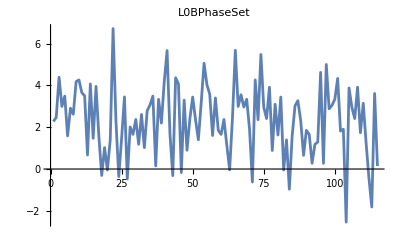
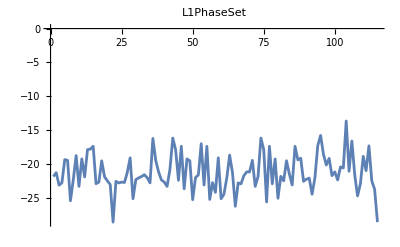
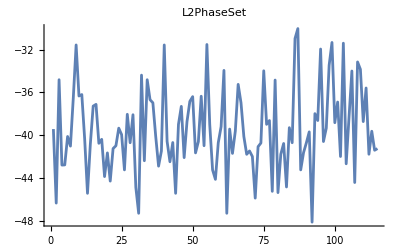
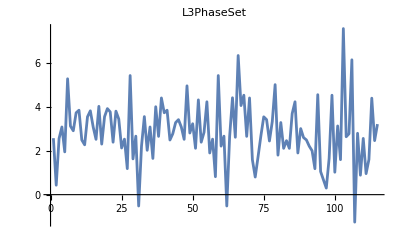
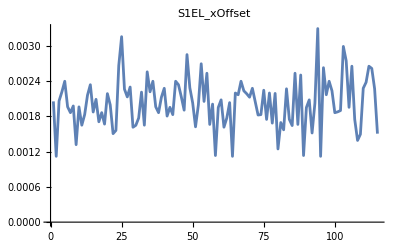
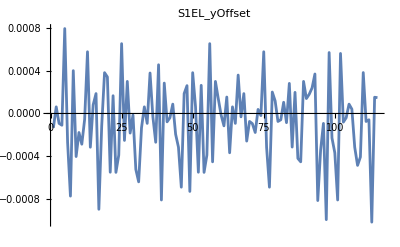
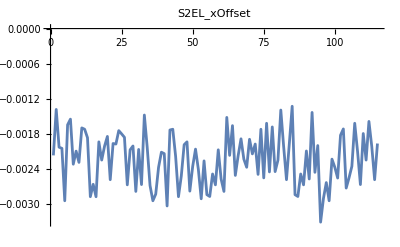
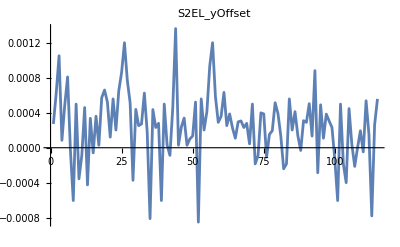
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | 0 | 0 | 0

```mathematica
imgArr=Table[
ListPlot[
raw[[All,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{L0BPhaseSet,L1PhaseSet,L2PhaseSet,L3PhaseSet,S1EL_xOffset,S1EL_yOffset,S1ER_xOffset,S1ER_yOffset,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}

```mathematica
fitVar = "PDrive_sigmaSI90_z"
```

PDrive_sigmaSI90_z

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

FittedModel[…]

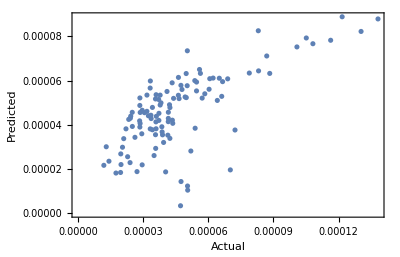

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
L0BPhaseSet | 1 | 2.86687×10^-10 | 2.86687×10^-10 | 0.818513 | 0.367834
L1PhaseSet | 1 | 6.26718×10^-11 | 6.26718×10^-11 | 0.178933 | 0.673219
L2PhaseSet | 1 | 2.88135×10^-8 | 2.88135×10^-8 | 82.2647 | 1.26182×10^-14
L3PhaseSet | 1 | 1.51284×10^-9 | 1.51284×10^-9 | 4.31928 | 0.0402961
S1ELxOffset | 1 | 8.38475×10^-10 | 8.38475×10^-10 | 2.39391 | 0.125032
S1ELyOffset | 1 | 9.62413×10^-11 | 9.62413×10^-11 | 0.274776 | 0.601329
S1ERxOffset | 1 | 5.33585×10^-11 | 5.33585×10^-11 | 0.152343 | 0.697154
S1ERyOffset | 1 | 4.65984×10^-11 | 4.65984×10^-11 | 0.133042 | 0.716084
S2ELxOffset | 1 | 4.91731×10^-10 | 4.91731×10^-10 | 1.40393 | 0.238932
S2ELyOffset | 1 | 1.20771×10^-10 | 1.20771×10^-10 | 0.344812 | 0.558415
S2ERxOffset | 1 | 3.12207×10^-12 | 3.12207×10^-12 | 0.00891376 | 0.924974
S2ERyOffset | 1 | 3.15979×10^-10 | 3.15979×10^-10 | 0.902144 | 0.344544
XC1FFkG | 1 | 1.60319×10^-11 | 1.60319×10^-11 | 0.0457722 | 0.831035
XC3FFkG | 1 | 1.21851×10^-10 | 1.21851×10^-10 | 0.347893 | 0.556666
YC1FFkG | 1 | 3.19034×10^-12 | 3.19034×10^-12 | 0.00910868 | 0.924161
YC2FFkG | 1 | 4.04452×10^-11 | 4.04452×10^-11 | 0.115474 | 0.734723
Error | 98 | 3.43248×10^-8 | 3.50253×10^-10 |  | 
Total | 114 | 6.71483×10^-8 |  |  |

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```